```mathematica
K[n_,0]:=K[n,0]=If[n==1,1,0]
K[n_,1]:=K[n,1]=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
K[n_,k_]:=K[n,k]=Sum[K[j,k-1]K[n/j,1],{j,Divisors[n]}]
PK[n_,k_] := Sum[ K[j,k],{j,2,n}]
d2[n_,k_]:=d2[n,k]=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=d2[n,1]=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1
D2[n_,k_] := D2[n,k]= Sum[ d2[j,k],{j,2,n}]
d[n_,k_]:=d[n,k]=Sum[d[j,k-1] d[n/j,1],{j,Divisors[n]}];d[n_,1]:=1;d[n_,0]:=0;d[1,0]:=1
c1:= CoefficientList[Series[ x/Log[1+x],{x,0,20}],x]
c2:= CoefficientList[Series[ x/Log[1-x],{x,0,20}],x]
```

```mathematica
q1[n_,1] := q1[n,1] = Sum[ c1[[k]] d2[n,k],{k,1,Log[2,n]}];q1[n_,0]:=q1[n,0]=If[n==1,1,0];q1[n_,k_] := q1[n,k]= Sum[q1[j,k-1] q1[n/j,1],{j,Divisors[n]}];q1[1,1]:=0
Q1[n_,k_] := Q1[n,k]=Sum[q1[j,k],{j,1,n}]
q2[n_,1] := q2[n,1] = Sum[ c2[[k]] d2[n,k],{k,1,Log[2,n]}];q2[n_,0]:=q2[n,0]=If[n==1,1,0];q2[n_,k_] := q2[n,k]= Sum[q2[j,k-1] q2[n/j,1],{j,Divisors[n]}];q2[1,1]:=0
Q2[n_,k_] := Q2[n,k]=Sum[q2[j,k],{j,1,n}]
q3[n_,1] := q3[n,1] = Sum[ c1[[k]] K[n,k],{k,1,Log[2,n]}];q3[n_,0]:=q3[n,0]=If[n==1,1,0];q3[n_,k_] := q3[n,k]= Sum[q3[j,k-1] q3[n/j,1],{j,Divisors[n]}];q3[1,1]:=0
Q3[n_,k_] := Q3[n,k]=Sum[q3[j,k],{j,1,n}]
q4[n_,1] := q4[n,1] = Sum[ c2[[k]] K[n,k],{k,1,Log[2,n]}];q4[n_,0]:=q4[n,0]=If[n==1,1,0];q4[n_,k_] := q4[n,k]= Sum[q4[j,k-1] q4[n/j,1],{j,Divisors[n]}];q4[1,1]:=0
Q4[n_,k_] := Q4[n,k]=Sum[q4[j,k],{j,1,n}]
```

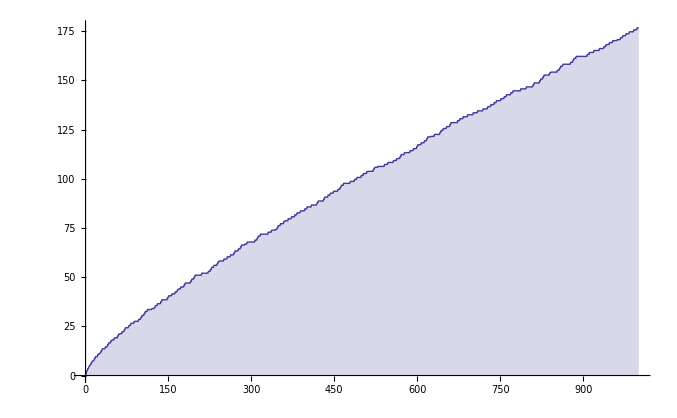

```mathematica
DiscretePlot[PK[n,1],{n,1,1000}]
```